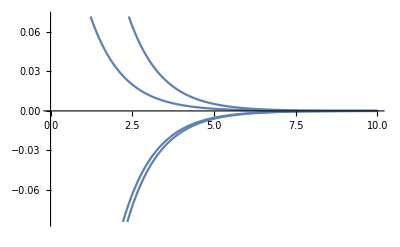

```mathematica
(* Simulating Matrix Differential Eqns*)
ClearAll["Global`*"];
tEnd=10;
X0=RandomReal[{-1,1},4];
A = ({{-1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}});
sol=x[t]/. NDSolve[{x'[t]==A.x[t],x[0]==X0},x,{t,0,tEnd}];
Plot[sol,{t,0,tEnd}]
```

```mathematica
Eigenvalues[A]
```

{-1.84525,0.370208,-0.272841,-0.0544376}